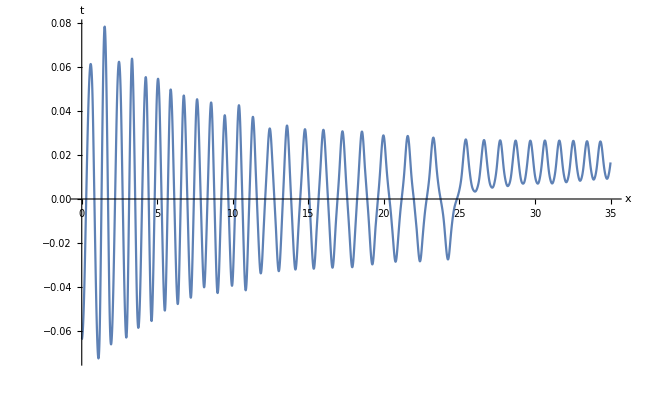

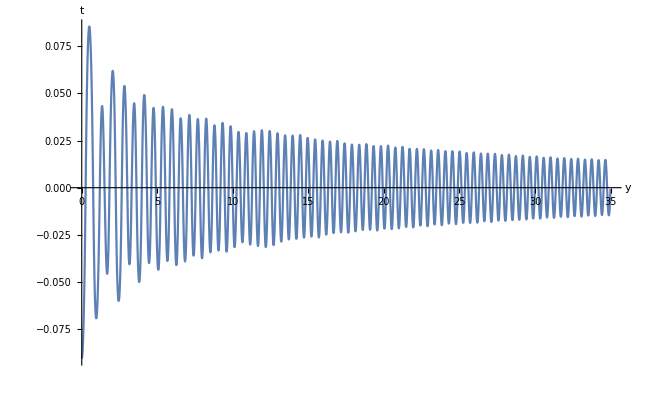

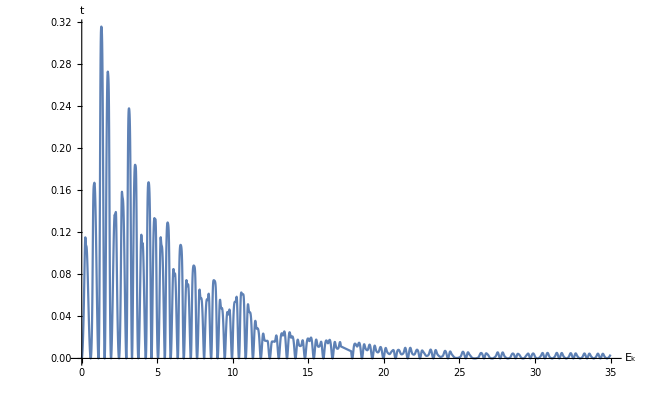

ParametricPlot::plld: {t,0,FE`tMax$$23} 中 t 的端点必须有不同的机器精度数值.

General::stop: 在本次计算中，ParametricPlot::plld 的进一步输出将被抑制.

ParametricPlot::plld: {t,0,FE`tMax$$23} 中 t 的端点必须有不同的机器精度数值.

General::stop: 在本次计算中，ParametricPlot::plld 的进一步输出将被抑制.

ParametricPlot::plld: {t,0,FE`tMax$$23} 中 t 的端点必须有不同的机器精度数值.

General::stop: 在本次计算中，ParametricPlot::plld 的进一步输出将被抑制.

ParametricPlot::plld: {t,0,0} 中 t 的端点必须有不同的机器精度数值.

ReplaceAll::reps: {sol} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ParametricPlot::plld: {t,0,0} 中 t 的端点必须有不同的机器精度数值.

ReplaceAll::reps: {NDSolve[{{0.05 (Times[«4»]+Times[«2»]),0.05 (Times[«4»]+Times[«3»])}=={-0.49 Sin[«1»]-3.22581 Plus[«2»]-0.00031 («1»)^(«1»)[«1»]-0.0197283 Power[«2»] («1»)^(«1»)[«1»],0.-0.00031 Sin[«1»] («1»)^(«1»)[«1»]-0.0197283 Sin[«1»] («1»)^(«1»)[«1»] Power[«2»]},x[0]==π/6,π/2[0]==1.25664,x'[0]==0.01,(π/2)'[0]==0.01},{x,π/2},{t,0,90}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ParametricPlot::plld: {t,0,0} 中 t 的端点必须有不同的机器精度数值.

ReplaceAll::reps: {sol} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

ParametricPlot::plld: {t,0,0} 中 t 的端点必须有不同的机器精度数值.

```mathematica
m=0.05;l=0.375;h=0.453;g=9.8;Subscript[k, 1]=0.0000;Subscript[k, 2]=0.02;μ=1.5;Subscript[R, 1]=0.04;Subscript[R, 2]=-0.04;
μ1={3μ Sin[x]Cos[y],3μ Sin[x]Sin[y],-3μ Cos[x]};
μ2={0,0,-3μ};
Subscript[r, 1]={l Sin[x]Cos[y]-Subscript[R, 1],l Sin[x]Sin[y],h-l Cos[x]};
Subscript[r, 2]={l Sin[x]Cos[y]-Subscript[R, 2],l Sin[x]Sin[y],h-l Cos[x]};
Subscript[f, 1]={-Subscript[k, 1] l x'[t],-Subscript[k, 1] l Sin[x[t]] y'[t]};
Subscript[f, 2]={-Subscript[k, 2] (l x'[t]+l Sin[x[t]] y'[t])^2*(l x'[t])/(((l x'[t]+l Sin[x[t]] y'[t])^2+(l x'[t]+l Sin[x[t]] y'[t])^2)^(1/2)),-Subscript[k, 2] (l x'[t]+l Sin[x[t]] y'[t])^2*(l Sin[x[t]] y'[t])/(((l x'[t]+l Sin[x[t]] y'[t])^2+(l x'[t]+l Sin[x[t]] y'[t])^2)^(1/2))};
G={-m g Sin[x[t]],0};
a={l x''[t]-l Sin[x[t]]Cos[x[t]] (y'[t])^2,l Sin[x[t]] y''[t]+2 l Cos[x[t]] x'[t] y'[t]};
V=-10^(-7)*(3(μ1.Subscript[r, 1])(μ2.Subscript[r, 1])-(Subscript[r, 1][[1]]^2+Subscript[r, 1][[2]]^2+Subscript[r, 1][[3]]^2)μ1.μ2)/((Subscript[r, 1][[1]]^2+Subscript[r, 1][[2]]^2+Subscript[r, 1][[3]]^2)^(5/2))-10^(-7)*(3(μ1.Subscript[r, 2])(μ2.Subscript[r, 2])-(Subscript[r, 2][[1]]^2+Subscript[r, 2][[2]]^2+Subscript[r, 2][[3]]^2)μ1.μ2)/((Subscript[r, 2][[1]]^2+Subscript[r, 2][[2]]^2+Subscript[r, 2][[3]]^2)^(5/2));
Subscript[F, M]={-D[V,x]/l,-D[V,y]/(l Sin[x])};
Subscript[f, M]=Subscript[F, M]/.{x->x[t],y->y[t]};
sol=NDSolve[{m a==G+Subscript[f, 1]+Subscript[f, 2]+Subscript[f, M],x[0]==0.3,y[0]==0.955338,x'[0]==0,y'[0]==0.00},{x,y},{t,0,35}];
Manipulate[ParametricPlot[Evaluate[{l Sin[x[t]]Cos[y[t]],l Sin[x[t]]Sin[y[t]]}/. sol],{t,0,tMax},PlotRange->All,AspectRatio->1/GoldenRatio,AxesLabel->{"x","y"},PlotStyle->{Red,Thickness[0.002]},Epilog->{Blue,PointSize[Large],Point[{l Sin[x[tMax]]Cos[y[tMax]],l Sin[x[tMax]]Sin[y[tMax]]}/. sol]}],{tMax,0,35}]
Plot[-l Sin[x[t]] Cos[y[t]]/. sol,{t,0,35},PlotRange->Full,AxesLabel->{"x","t"}]
Plot[-l Sin[x[t]] Sin[y[t]]/. sol,{t,0,35},PlotRange->Full,AxesLabel->{"y","t"}]
Plot[{(l Cos[x[t]] x'[t] Cos[y[t]]-l Sin[x[t]] Sin[y[t]] y'[t])^2/. sol},{t,0,35},PlotRange->Full,AxesLabel->{"E_k","t"}]
```

```mathematica
Clear["Global`*"]
```